## Shear Analysis

L: | 80.1
m: | 400
kappa: | 6.
sigma: | 0.000267
kappa_sigma_r: | 22497.2
Delta: | 0.1
Extension Minimum: | 0
Extension Maximum: | 150
beta: | 4.
mu: | 0.01
c: | 0.14
delta: | 4.3
b: | 0.38
k: | 0.07
ev0: | 1.71
C0: | 0.23
e0: | 0.005001
beta: | 38.6817

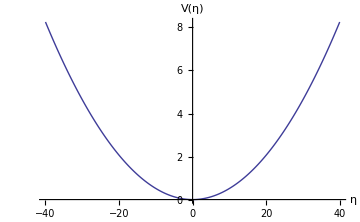

0.005001

Backbone spring constant κ:

6.

Residue-pair spring constant σ(ϵ = 0.005001):

0.000267

κ/σ ratio:

22497.2

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

PotentialData = Import["potential_data.out","Table"];

PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];

Subscript[R, pfmxd]=Import["pfmxd_r.out","Table"];
Subscript[R, mxd]=Import["mxd_r.out","Table"];

Subscript[λ, pfmxd]=Import["pfmxd_lambda.out","Table"];
Subscript[λ, mxd]=Import["mxd_lambda.out","Table"];

Subscript[ρ, pfmxd]=Import["pfmxd_roe.out","Table"];
Subscript[ρ, mxd]=Import["mxd_roe.out","Table"];

Parameters=Import["Parameters"];
Grid[Parameters]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]

ϵ=Parameters[[17,2]]
β=Parameters[[18,2]];

L=Parameters[[1,2]];
m=Parameters[[2,2]];
Δ=Parameters[[6,2]];
Print["Backbone spring constant κ:"]
κ=Parameters[[3,2]]
Print["Residue-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[4,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[5,2]]
umax=Parameters[[7,2]];
umax=Parameters[[8,2]];

n=ToExpression[StringTrim[Last[StringSplit[Directory[],"/"]],RegularExpression["N*"]]];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

Subscript[η, B]=4;

ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f (κ/(2β))^(1/2)) ToNewton;
ToDimension[η_]:=η ((κ β)/2)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]](*Å*)
```

4

0.371319

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

0.158843

223.094

Partition function & Free Energy

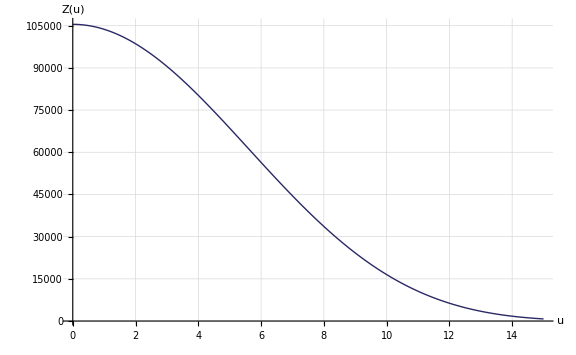
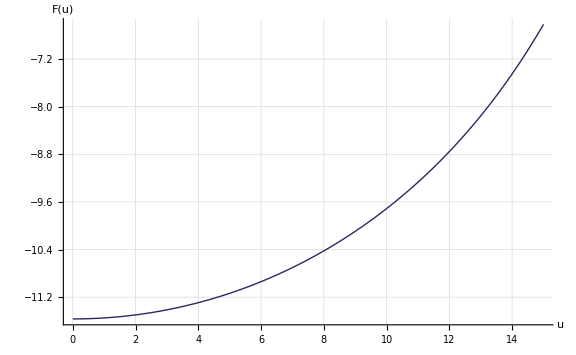

```mathematica
pIntactPF=ListLinePlot[PartitionFunction,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["Z(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

pIntactFE=ListLinePlot[FreeEnergy,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

{pIntactPF,pIntactFE}
```

Residue-pair separations (x-z), (x-y), (z-y)

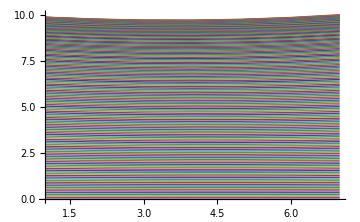
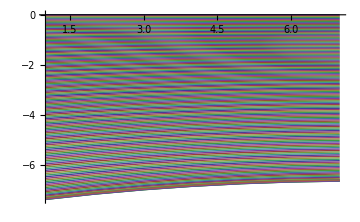

3.97811

0 | 0 | 0 | 0 | 0 | 0 | 0
0.0933478 | 0.0919546 | 0.0910356 | 0.0905862 | 0.0906041 | 0.0910894 | 0.0920445
0.186693 | 0.183907 | 0.18207 | 0.181171 | 0.181207 | 0.182178 | 0.184089
0.280035 | 0.275856 | 0.273101 | 0.271754 | 0.271809 | 0.273266 | 0.276132
0.37337 | 0.3678 | 0.364127 | 0.362333 | 0.362408 | 0.364352 | 0.368175
0.466696 | 0.459736 | 0.455148 | 0.452907 | 0.453003 | 0.455435 | 0.460217
0.560011 | 0.551663 | 0.546161 | 0.543476 | 0.543594 | 0.546516 | 0.552257
0.653313 | 0.643579 | 0.637164 | 0.634037 | 0.634179 | 0.637593 | 0.644296
0.7466 | 0.735482 | 0.728157 | 0.724589 | 0.724758 | 0.728666 | 0.736332
0.839869 | 0.827369 | 0.819137 | 0.815131 | 0.815329 | 0.819733 | 0.828365
0.933117 | 0.91924 | 0.910103 | 0.905662 | 0.905892 | 0.910795 | 0.920395
1.02634 | 1.01109 | 1.00105 | 0.99618 | 0.996444 | 1.00185 | 1.01242
1.11954 | 1.10292 | 1.09199 | 1.08668 | 1.08699 | 1.0929 | 1.10444
1.21272 | 1.19473 | 1.1829 | 1.17717 | 1.17752 | 1.18393 | 1.19646
1.30586 | 1.28651 | 1.27379 | 1.26764 | 1.26803 | 1.27496 | 1.28847
1.39897 | 1.37826 | 1.36465 | 1.35809 | 1.35853 | 1.36598 | 1.38047
1.49205 | 1.46998 | 1.4555 | 1.44852 | 1.44901 | 1.45698 | 1.47247
1.58508 | 1.56167 | 1.54631 | 1.53892 | 1.53948 | 1.54797 | 1.56445
1.67808 | 1.65332 | 1.63709 | 1.6293 | 1.62992 | 1.63895 | 1.65643
1.77103 | 1.74493 | 1.72784 | 1.71965 | 1.72034 | 1.7299 | 1.74839
1.86393 | 1.8365 | 1.81855 | 1.80998 | 1.81074 | 1.82084 | 1.84034
1.95678 | 1.92803 | 1.90922 | 1.90026 | 1.90111 | 1.91176 | 1.93227
2.04958 | 2.01951 | 1.99986 | 1.99052 | 1.99145 | 2.00265 | 2.02419
2.14232 | 2.11093 | 2.09044 | 2.08074 | 2.08176 | 2.09352 | 2.11608
2.23499 | 2.20231 | 2.18098 | 2.17091 | 2.17204 | 2.18436 | 2.20796
2.3276 | 2.29362 | 2.27148 | 2.26104 | 2.26227 | 2.27518 | 2.29981
2.42014 | 2.38488 | 2.36191 | 2.35113 | 2.35247 | 2.36595 | 2.39164
2.51261 | 2.47606 | 2.45229 | 2.44116 | 2.44263 | 2.4567 | 2.48343
2.605 | 2.56718 | 2.54261 | 2.53115 | 2.53274 | 2.5474 | 2.5752
2.69731 | 2.65823 | 2.63286 | 2.62107 | 2.6228 | 2.63806 | 2.66693
2.78953 | 2.7492 | 2.72304 | 2.71093 | 2.71281 | 2.72867 | 2.75862
2.88166 | 2.84008 | 2.81315 | 2.80073 | 2.80276 | 2.81924 | 2.85027
2.9737 | 2.93088 | 2.90318 | 2.89046 | 2.89265 | 2.90975 | 2.94187
3.06563 | 3.02159 | 2.99313 | 2.98011 | 2.98247 | 3.00021 | 3.03342
3.15745 | 3.1122 | 3.08299 | 3.06969 | 3.07222 | 3.0906 | 3.12492
3.24917 | 3.2027 | 3.17276 | 3.15918 | 3.1619 | 3.18093 | 3.21636
3.34076 | 3.2931 | 3.26243 | 3.24859 | 3.2515 | 3.27118 | 3.30774
3.43224 | 3.38339 | 3.352 | 3.33789 | 3.34101 | 3.36136 | 3.39905
3.52358 | 3.47356 | 3.44146 | 3.42711 | 3.43043 | 3.45145 | 3.49028
3.61478 | 3.5636 | 3.5308 | 3.51621 | 3.51976 | 3.54146 | 3.58144
3.70585 | 3.65351 | 3.62002 | 3.6052 | 3.60898 | 3.63138 | 3.67251
3.79676 | 3.74328 | 3.70912 | 3.69408 | 3.6981 | 3.7212 | 3.76349
3.88752 | 3.83291 | 3.79808 | 3.78283 | 3.7871 | 3.81091 | 3.85437
3.97811 | 3.92239 | 3.8869 | 3.87146 | 3.87598 | 3.90051 | 3.94515
4.06853 | 4.0117 | 3.97557 | 3.95994 | 3.96474 | 3.98999 | 4.03582
4.15877 | 4.10085 | 4.06408 | 4.04828 | 4.05335 | 4.07934 | 4.12636
4.24883 | 4.18983 | 4.15244 | 4.13646 | 4.14183 | 4.16856 | 4.21679
4.33869 | 4.27862 | 4.24062 | 4.22449 | 4.23015 | 4.25763 | 4.30708
4.42835 | 4.36722 | 4.32862 | 4.31234 | 4.31831 | 4.34656 | 4.39722
4.5178 | 4.45562 | 4.41643 | 4.40002 | 4.40631 | 4.43532 | 4.48722
4.60702 | 4.54382 | 4.50405 | 4.48751 | 4.49413 | 4.52392 | 4.57705
4.69602 | 4.63179 | 4.59146 | 4.57481 | 4.58176 | 4.61234 | 4.66672
4.78477 | 4.71954 | 4.67866 | 4.6619 | 4.6692 | 4.70058 | 4.7562
4.87328 | 4.80705 | 4.76563 | 4.74878 | 4.75643 | 4.78861 | 4.8455
4.96152 | 4.89432 | 4.85236 | 4.83543 | 4.84345 | 4.87644 | 4.9346
5.0495 | 4.98133 | 4.93885 | 4.92185 | 4.93024 | 4.96406 | 5.02348
5.13719 | 5.06806 | 5.02508 | 5.00802 | 5.01679 | 5.05144 | 5.11215
5.22459 | 5.15453 | 5.11105 | 5.09394 | 5.1031 | 5.13859 | 5.20058
5.31169 | 5.2407 | 5.19674 | 5.17959 | 5.18915 | 5.22548 | 5.28877
5.39847 | 5.32657 | 5.28214 | 5.26495 | 5.27493 | 5.31211 | 5.3767
5.48493 | 5.41212 | 5.36723 | 5.35003 | 5.36042 | 5.39847 | 5.46436
5.57104 | 5.49735 | 5.45201 | 5.4348 | 5.44562 | 5.48453 | 5.55173
5.65681 | 5.58224 | 5.53647 | 5.51926 | 5.53051 | 5.5703 | 5.63881
5.74221 | 5.66678 | 5.62059 | 5.60338 | 5.61508 | 5.65575 | 5.72558
5.82723 | 5.75096 | 5.70435 | 5.68716 | 5.69931 | 5.74086 | 5.81203
5.91186 | 5.83475 | 5.78774 | 5.77059 | 5.7832 | 5.82564 | 5.89813
5.99608 | 5.91816 | 5.87076 | 5.85364 | 5.86672 | 5.91006 | 5.98388
6.07989 | 6.00116 | 5.95338 | 5.93631 | 5.94986 | 5.9941 | 6.06926
6.16326 | 6.08373 | 6.03559 | 6.01857 | 6.0326 | 6.07775 | 6.15425
6.24618 | 6.16587 | 6.11737 | 6.10042 | 6.11494 | 6.161 | 6.23884
6.32864 | 6.24757 | 6.19871 | 6.18184 | 6.19685 | 6.24383 | 6.32301
6.41062 | 6.32879 | 6.2796 | 6.26281 | 6.27832 | 6.32621 | 6.40674
6.4921 | 6.40953 | 6.36002 | 6.34331 | 6.35933 | 6.40815 | 6.49002
6.57307 | 6.48977 | 6.43995 | 6.42334 | 6.43986 | 6.48961 | 6.57282
6.65352 | 6.5695 | 6.51937 | 6.50286 | 6.5199 | 6.57057 | 6.65514
6.73341 | 6.64869 | 6.59826 | 6.58187 | 6.59943 | 6.65103 | 6.73694
6.81275 | 6.72733 | 6.67662 | 6.66035 | 6.67843 | 6.73096 | 6.81821
6.8915 | 6.80541 | 6.75442 | 6.73827 | 6.75688 | 6.81034 | 6.89893
6.96966 | 6.8829 | 6.83164 | 6.81562 | 6.83476 | 6.88915 | 6.97908
7.0472 | 6.95979 | 6.90827 | 6.89239 | 6.91206 | 6.96738 | 7.05864
7.12411 | 7.03605 | 6.98428 | 6.96854 | 6.98874 | 7.045 | 7.13759
7.20036 | 7.11167 | 7.05966 | 7.04407 | 7.06481 | 7.12199 | 7.21591
7.27595 | 7.18663 | 7.13439 | 7.11894 | 7.14022 | 7.19833 | 7.29357
7.35083 | 7.26091 | 7.20844 | 7.19315 | 7.21496 | 7.27399 | 7.37055
7.42501 | 7.33449 | 7.28179 | 7.26666 | 7.28902 | 7.34897 | 7.44683
7.49846 | 7.40734 | 7.35444 | 7.33947 | 7.36236 | 7.42323 | 7.52239
7.57115 | 7.47946 | 7.42635 | 7.41154 | 7.43497 | 7.49675 | 7.5972
7.64307 | 7.55081 | 7.4975 | 7.48286 | 7.50682 | 7.56951 | 7.67124
7.71419 | 7.62137 | 7.56787 | 7.5534 | 7.5779 | 7.64148 | 7.74448
7.7845 | 7.69114 | 7.63744 | 7.62315 | 7.64817 | 7.71265 | 7.8169
7.85397 | 7.76007 | 7.70619 | 7.69207 | 7.71762 | 7.78298 | 7.88848
7.92259 | 7.82815 | 7.7741 | 7.76014 | 7.78622 | 7.85245 | 7.95919
7.99032 | 7.89537 | 7.84114 | 7.82735 | 7.85394 | 7.92105 | 8.02901
8.05715 | 7.96168 | 7.90728 | 7.89367 | 7.92077 | 7.98874 | 8.0979
8.12306 | 8.02708 | 7.97252 | 7.95907 | 7.98668 | 8.05549 | 8.16585
8.18801 | 8.09155 | 8.03681 | 8.02354 | 8.05165 | 8.12129 | 8.23283
8.252 | 8.15504 | 8.10015 | 8.08704 | 8.11564 | 8.18611 | 8.2988
8.315 | 8.21756 | 8.1625 | 8.14956 | 8.17864 | 8.24992 | 8.36375
8.37697 | 8.27906 | 8.22385 | 8.21106 | 8.24062 | 8.3127 | 8.42765
8.43791 | 8.33953 | 8.28416 | 8.27153 | 8.30156 | 8.37441 | 8.49046
8.49779 | 8.39894 | 8.34342 | 8.33094 | 8.36143 | 8.43505 | 8.55217
8.55658 | 8.45728 | 8.4016 | 8.38926 | 8.4202 | 8.49457 | 8.61275
8.61426 | 8.51451 | 8.45868 | 8.44648 | 8.47785 | 8.55295 | 8.67217
8.6708 | 8.57061 | 8.51462 | 8.50256 | 8.53435 | 8.61017 | 8.7304
8.72619 | 8.62556 | 8.56942 | 8.55749 | 8.58969 | 8.6662 | 8.78741
8.78041 | 8.67934 | 8.62305 | 8.61123 | 8.64383 | 8.72102 | 8.84319
8.83342 | 8.73192 | 8.67547 | 8.66377 | 8.69675 | 8.77459 | 8.8977
8.88521 | 8.78329 | 8.72667 | 8.71507 | 8.74843 | 8.82691 | 8.95092
8.93575 | 8.83341 | 8.77663 | 8.76513 | 8.79883 | 8.87793 | 9.00282
8.98502 | 8.88226 | 8.82532 | 8.81391 | 8.84795 | 8.92764 | 9.05337
9.033 | 8.92983 | 8.87273 | 8.86138 | 8.89575 | 8.97601 | 9.10256
9.07968 | 8.9761 | 8.91882 | 8.90754 | 8.94222 | 9.02302 | 9.15036
9.12501 | 9.02103 | 8.96358 | 8.95236 | 8.98732 | 9.06864 | 9.19674
9.169 | 9.06462 | 9.00699 | 8.99582 | 9.03105 | 9.11287 | 9.24169
9.21162 | 9.10683 | 9.04902 | 9.03789 | 9.07337 | 9.15566 | 9.28518
9.25284 | 9.14766 | 9.08967 | 9.07856 | 9.11428 | 9.19701 | 9.32719
9.29266 | 9.18709 | 9.12891 | 9.11781 | 9.15375 | 9.2369 | 9.3677
9.33106 | 9.22509 | 9.16672 | 9.15563 | 9.19176 | 9.27531 | 9.4067
9.36801 | 9.26167 | 9.20309 | 9.19199 | 9.22831 | 9.31223 | 9.44418
9.40351 | 9.29679 | 9.23802 | 9.2269 | 9.26337 | 9.34763 | 9.48011
9.43755 | 9.33044 | 9.27147 | 9.26033 | 9.29695 | 9.38152 | 9.51449
9.4701 | 9.36263 | 9.30346 | 9.29227 | 9.32901 | 9.41388 | 9.5473
9.50118 | 9.39334 | 9.33396 | 9.32272 | 9.35957 | 9.44471 | 9.57855
9.53076 | 9.42256 | 9.36297 | 9.35168 | 9.38862 | 9.47399 | 9.60823
9.55884 | 9.45029 | 9.39049 | 9.37913 | 9.41615 | 9.50174 | 9.63634
9.58542 | 9.47653 | 9.41653 | 9.40509 | 9.44217 | 9.52795 | 9.66288
9.61051 | 9.50128 | 9.44107 | 9.42956 | 9.46668 | 9.55264 | 9.68787
9.6341 | 9.52455 | 9.46414 | 9.45254 | 9.4897 | 9.57581 | 9.71131
9.6562 | 9.54635 | 9.48573 | 9.47405 | 9.51123 | 9.59748 | 9.73323
9.67683 | 9.56668 | 9.50588 | 9.4941 | 9.53131 | 9.61767 | 9.75365
9.696 | 9.58557 | 9.52459 | 9.51273 | 9.54994 | 9.63641 | 9.77259
9.71374 | 9.60304 | 9.54189 | 9.52995 | 9.56717 | 9.65374 | 9.7901
9.73006 | 9.61913 | 9.55781 | 9.5458 | 9.58303 | 9.66969 | 9.80623
9.74499 | 9.63385 | 9.5724 | 9.56033 | 9.59758 | 9.68433 | 9.82103
9.75859 | 9.64727 | 9.58571 | 9.57359 | 9.61085 | 9.69769 | 9.83456
9.77089 | 9.65942 | 9.59777 | 9.58563 | 9.62293 | 9.70987 | 9.8469
9.78195 | 9.67036 | 9.60866 | 9.59652 | 9.63388 | 9.72094 | 9.85814
9.79182 | 9.68017 | 9.61845 | 9.60635 | 9.6438 | 9.73099 | 9.86838
9.80058 | 9.68892 | 9.62723 | 9.6152 | 9.65277 | 9.74013 | 9.87773
9.80832 | 9.6967 | 9.63509 | 9.62319 | 9.66092 | 9.74849 | 9.88634
9.81512 | 9.70361 | 9.64215 | 9.63042 | 9.66838 | 9.7562 | 9.89434
9.8211 | 9.70977 | 9.64852 | 9.63705 | 9.67528 | 9.76342 | 9.90192
9.82637 | 9.71531 | 9.65436 | 9.64322 | 9.68181 | 9.77034 | 9.90927
9.83107 | 9.72038 | 9.65982 | 9.6491 | 9.68814 | 9.77716 | 9.91661
9.83535 | 9.72514 | 9.66509 | 9.65489 | 9.69449 | 9.78411 | 9.92418
9.83939 | 9.72977 | 9.67035 | 9.66081 | 9.7011 | 9.79143 | 9.93227
9.84336 | 9.7345 | 9.67585 | 9.6671 | 9.70823 | 9.79942 | 9.94117
9.84749 | 9.73953 | 9.68182 | 9.67404 | 9.71616 | 9.8084 | 9.95124
9.852 | 9.74514 | 9.68854 | 9.68192 | 9.72523 | 9.81872 | 9.96285
9.85715 | 9.75158 | 9.69632 | 9.69107 | 9.7358 | 9.83076 | 9.97642
9.86321 | 9.75918 | 9.70548 | 9.70185 | 9.74826 | 9.84495 | 9.99243

Extension U (End base-pair separations at η_B) = 43

Extension U in terms of η = 4.3 (43Δ)

```mathematica
xzpair=-(√3 Subscript[λ, mxd]+Subscript[ρ, mxd])/(√2);
xypair=√2 Subscript[ρ, mxd];

{ListLinePlot[xzpair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],ListLinePlot[xypair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[xzpair,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[xzpair,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[xzpair,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at \!\(\*SubscriptBox[\"η\", \"B\"]\)) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

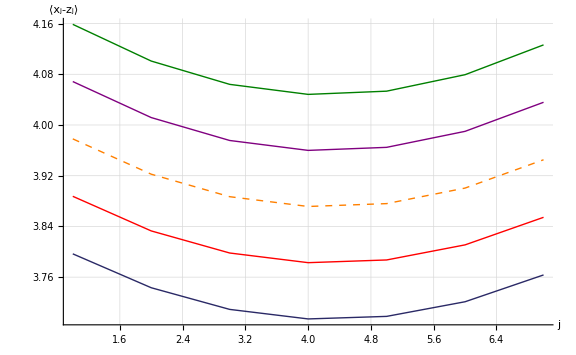
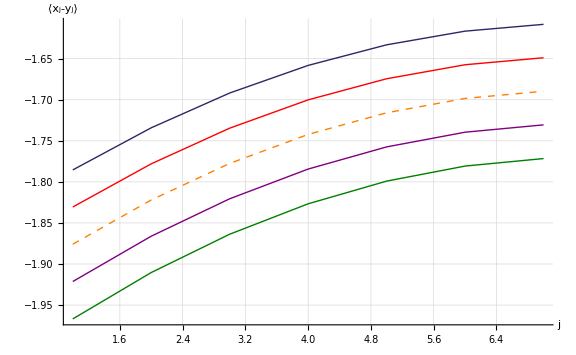

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pxzpair=ListLinePlot[{xzpair[[pos1]],xzpair[[pos2]],xzpair[[pos3]],xzpair[[pos4]],xzpair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-z_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

pxypair=ListLinePlot[{xypair[[pos1]],xypair[[pos2]],xypair[[pos3]],xypair[[pos4]],xypair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-y_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

{pxzpair,pxypair}
```

### Force-Extension

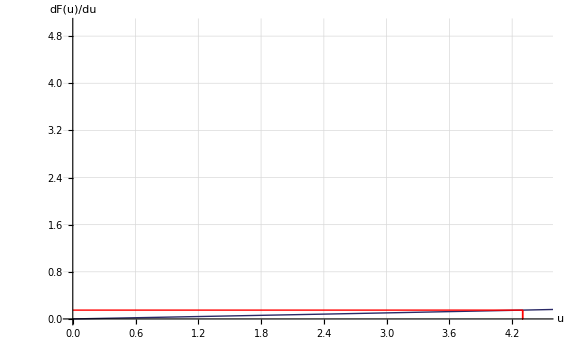

Dimensionless force at (U = 43Δ) = 0.149665

Dimensional Force = 66.7789 pN
Dimensional Extension = 0.399167 Å

```mathematica
fpos={{0,dFreeEnergy[[upos]][[2]]},{dFreeEnergy[[upos]][[1]],dFreeEnergy[[upos]][[2]]},{dFreeEnergy[[upos]][[1]],0},{dFreeEnergy[[upos]][[1]],dFreeEnergy[[upos]][[2]]}};
F=dFreeEnergy[[upos]][[2]];
u=dFreeEnergy[[upos]][[1]];

p=ListLinePlot[{dFreeEnergy,fpos},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red}},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->{{0,Δ(upos+1)},{0,5}},AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["dF(u)/du",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}]

Print["Dimensionless force at (U = ",U,"Δ) = ",F]

Fc=ToForceDimension[F];
Print["\nDimensional Force = ",Fc pN,"\nDimensional Extension = ",ToDimension[u] Å,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Fc,NearestValue,κσr}},"Table"];
```